## With the prior g > 0

The likelihood function is Gaussian in g^n with n 1, 2, 4 for the cases we’re interested in. Defining a dimensionless variable that is g divided by the nth root of the variance in the Gaussian likelihood and normalizing, the posterior over the parameter g is:

```mathematica
gaus=(1/((2)^(1/(2 n)) Gamma[1+1/(2 n)])Exp[-g^(2 n)/2])/.n->1;
quad=(1/((2)^(1/(2 n)) Gamma[1+1/(2 n)])Exp[-g^(2 n)/2])/.n->2;
oct=(1/((2)^(1/(2 n)) Gamma[1+1/(2 n)])Exp[-g^(2 n)/2])/.n->4;
```

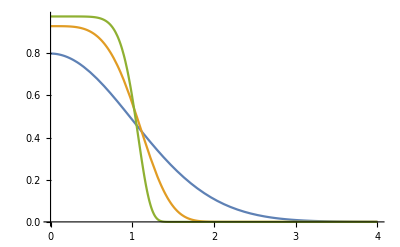

```mathematica
Plot[{gaus,quad,oct},{g,0,4}]
```

You can compute the value of g that yields 68 percent of the area under the curves:

```mathematica
NIntegrate[gaus,{g,0,1}]
```

0.682689

```mathematica
sigma=x/.FindRoot[NIntegrate[quad,{g,0,x}]==0.6826894921370867,{x,0.5}]
NIntegrate[quad,{g,0,sigma}]
```

0.760113

0.682689

```mathematica
sigma=x/.FindRoot[NIntegrate[oct,{g,0,x}]==0.6826894921370867,{x,0.5}]
NIntegrate[oct,{g,0,sigma}]
```

0.703431

0.682689

This means that for n=2 the constraint is a factor of 0.76 times the 1/4 root of the SNR and for n=4 the constraint is a factor of 0.7 times the 1/8 root of the SNR. These factors indeed disagree with what we had in the dark photon paper. For fun, here are the 99.7 percent (3 sigma) limits which should have a larger difference:

```mathematica
NIntegrate[gaus,{g,0,3}]
```

0.9973

```mathematica
NIntegrate[quad,{g,0,1.63}]
```

0.997329

```mathematica
NIntegrate[oct,{g,0,1.24}]
```

0.997363

You can also compute the standard deviation:

```mathematica
meangaus=Integrate[g gaus,{g,0,Infinity}]//N
vargaus=1. Integrate[(g-meangaus)^2 gaus,{g,0,Infinity}];
stdgaus=Sqrt[vargaus]
```

0.797885

0.60281

```mathematica
meanquad=Integrate[g quad,{g,0,Infinity}]//N
varquad=1. Integrate[(g-meanquad)^2 quad,{g,0,Infinity}];
stdquad=Sqrt[varquad]
stdquad/stdgaus
```

0.581368

0.374165

0.620702

```mathematica
meanoct=Integrate[g oct,{g,0,Infinity}]//N
varoct=1. Integrate[(g-meanoct)^2 oct,{g,0,Infinity}];
stdoct=Sqrt[varoct]
stdoct/stdgaus
```

0.524792

0.314258

0.521322

## Without the prior g > 0

The likelihood function is Gaussian in g^n with n 1, 2, 4 for the cases we’re interested in. Defining a dimensionless variable that is g divided by the nth root of the variance in the Gaussian likelihood and normalizing, the posterior over the parameter g is:

```mathematica
gaus=(1/(2 2^(1/(2n)) Gamma[1+1/(2 n)])Exp[-g^(2 n)/2])/.n->1;
quad=(1/(2 2^(1/(2n)) Gamma[1+1/(2 n)])Exp[-g^(2 n)/2])/.n->2;
oct=(1/(2 2^(1/(2n)) Gamma[1+1/(2 n)])Exp[-g^(2 n)/2])/.n->4;
```

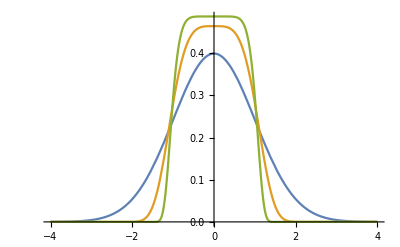

```mathematica
Plot[{gaus,quad,oct},{g,-4,4}]
```

You can compute the value of g that yields 68 percent of the area under the curves:

```mathematica
FindRoot[NIntegrate[gaus,{g,0,x}]==0.341,{x,0.5}]
```

{x→0.998576}

```mathematica
NIntegrate[gaus,{g,0,1}]
```

0.341345

```mathematica
FindRoot[NIntegrate[quad,{g,0,x}]==0.341,{x,0.5}]
```

{x→0.759235}

```mathematica
NIntegrate[quad,{g,0,0.7592348532167482}]
```

0.341

```mathematica
FindRoot[NIntegrate[oct,{g,0,x}]==0.341,{x,0.5}]
```

{x→0.702702}

```mathematica
NIntegrate[oct,{g,0,0.702701599507406}]
```

0.341

You can also compute the standard deviation:

```mathematica
meangaus=Integrate[g gaus,{g,-Infinity,Infinity}]//N
vargaus=1. Integrate[(g-meangaus)^2 gaus,{g,-Infinity,Infinity}];
stdgaus=Sqrt[vargaus]
```

0.

1.

```mathematica
meanquad=Integrate[g quad,{g,-Infinity,Infinity}]//N
varquad=1. Integrate[(g-meanquad)^2 quad,{g,-Infinity,Infinity}];
stdquad=Sqrt[varquad]
stdquad/stdgaus
```

0.

0.691367

0.691367

```mathematica
meanoct=Integrate[g oct,{g,-Infinity,Infinity}]//N
varoct=1. Integrate[(g-meanoct)^2 oct,{g,-Infinity,Infinity}];
stdoct=Sqrt[varoct]
stdoct/stdgaus
```

0.

0.611691

0.611691